```mathematica
(* TB Incidence data for each year *)
```

```mathematica
s4={{27,10},{42,16},{57,35},{72,108},{89,174}}
```

{{27,10},{42,16},{57,35},{72,108},{89,174}}

```mathematica
s5={{27,10},{42,15},{57,31},{72,95},{89,176}}
```

{{27,10},{42,15},{57,31},{72,95},{89,176}}

```mathematica
s6={{27,10},{42,15},{57,30},{72,92},{89,175}}
```

{{27,10},{42,15},{57,30},{72,92},{89,175}}

```mathematica
s7={{27,9},{42,14},{57,26},{72,86},{89,178}}
```

{{27,9},{42,14},{57,26},{72,86},{89,178}}

```mathematica
s8={{27,9},{42,12},{57,23},{72,74},{89,148}}
```

{{27,9},{42,12},{57,23},{72,74},{89,148}}

```mathematica
s9={{27,7},{42,11},{57,20},{72,65},{89,142}}
```

{{27,7},{42,11},{57,20},{72,65},{89,142}}

```mathematica
inc4=Table[{s4[[i,1]],300/96 s4[[i,2]]},{i,Length[s4]}]
inc5=Table[{s4[[i,1]],300/96 s5[[i,2]]},{i,Length[s4]}]
inc6=Table[{s4[[i,1]],300/96 s6[[i,2]]},{i,Length[s4]}]
inc7=Table[{s4[[i,1]],300/96 s7[[i,2]]},{i,Length[s4]}]
inc8=Table[{s4[[i,1]],300/96 s8[[i,2]]},{i,Length[s4]}]
inc9=Table[{s4[[i,1]],300/96 s9[[i,2]]},{i,Length[s4]}]
```

{{27,125/4},{42,50},{57,875/8},{72,675/2},{89,2175/4}}

{{27,125/4},{42,375/8},{57,775/8},{72,2375/8},{89,550}}

{{27,125/4},{42,375/8},{57,375/4},{72,575/2},{89,4375/8}}

{{27,225/8},{42,175/4},{57,325/4},{72,1075/4},{89,2225/4}}

{{27,225/8},{42,75/2},{57,575/8},{72,925/4},{89,925/2}}

{{27,175/8},{42,275/8},{57,125/2},{72,1625/8},{89,1775/4}}

```mathematica
(* Taking Logs *)
```

```mathematica
inclog4=Table[{s4[[i,1]],Log[300/96 s4[[i,2]]]},{i,Length[s4]}]
inclog5=Table[{s4[[i,1]],Log[300/96 s5[[i,2]]]},{i,Length[s4]}]
inclog6=Table[{s4[[i,1]],Log[300/96 s6[[i,2]]]},{i,Length[s4]}]
inclog7=Table[{s4[[i,1]],Log[300/96 s7[[i,2]]]},{i,Length[s4]}]
inclog8=Table[{s4[[i,1]],Log[300/96 s8[[i,2]]]},{i,Length[s4]}]
inclog9=Table[{s4[[i,1]],Log[300/96 s9[[i,2]]]},{i,Length[s4]}]
```

{{27,Log[125/4]},{42,Log[50]},{57,Log[875/8]},{72,Log[675/2]},{89,Log[2175/4]}}

{{27,Log[125/4]},{42,Log[375/8]},{57,Log[775/8]},{72,Log[2375/8]},{89,Log[550]}}

{{27,Log[125/4]},{42,Log[375/8]},{57,Log[375/4]},{72,Log[575/2]},{89,Log[4375/8]}}

{{27,Log[225/8]},{42,Log[175/4]},{57,Log[325/4]},{72,Log[1075/4]},{89,Log[2225/4]}}

{{27,Log[225/8]},{42,Log[75/2]},{57,Log[575/8]},{72,Log[925/4]},{89,Log[925/2]}}

{{27,Log[175/8]},{42,Log[275/8]},{57,Log[125/2]},{72,Log[1625/8]},{89,Log[1775/4]}}

```mathematica
inc=(inc4+inc5+inc6+inc7+inc8+inc9)/6
```

{{27,1375/48},{42,2075/48},{57,1375/16},{72,1625/6},{89,8275/16}}

```mathematica
Ages2=Range[5,85,5]
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85}

```mathematica
mexpshort=Table[Exp[0.044Ages2[[i]]]/10,{i,Length[Ages2]}]
```

{0.124608,0.155271,0.193479,0.24109,0.300417,0.374342,0.466459,0.581244,0.724274,0.902501,1.12459,1.40132,1.74615,2.17584,2.71126,3.37844,4.2098}

```mathematica
Ems=DiagonalMatrix[mexpshort]
```

{{0.124608,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.155271,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.193479,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.24109,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.300417,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.374342,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.466459,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.581244,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.724274,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.902501,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.12459,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.40132,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.74615,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.17584,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.71126,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.37844,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.2098}}

```mathematica
FRACMreg=Drop[Drop[Import["~/Projects/TB/CM/TaiwanCM.csv"],1,1],0,-3]
```

{{1.35632,0.655172,0.172414,0.0574713,0.298851,0.678161,1.56322,1.14943,0.413793,0.264368,0.413793,0.528736,0.689655,0.333333,0.149425,0.045977,0.0689655},{0.330275,9.51376,1.20183,0.211009,0.155963,0.568807,1.10092,1.33945,1.06422,0.40367,0.275229,0.330275,0.385321,0.284404,0.165138,0.0825688,0.0642202},{0.0955882,0.735294,10.7794,0.919118,0.154412,0.433824,0.404412,0.875,1.08824,0.654412,0.352941,0.147059,0.257353,0.169118,0.154412,0.125,0.102941},{0.0740741,0.135802,0.679012,7.75309,0.537037,0.506173,0.561728,0.679012,0.845679,1.12346,0.728395,0.179012,0.166667,0.0802469,0.141975,0.0987654,0.141975},{0.118644,0.101695,0.322034,0.855932,4.41525,1.81356,0.932203,0.855932,0.686441,0.79661,1.00847,0.254237,0.118644,0.110169,0.118644,0.059322,0.101695},{0.287879,0.204545,0.174242,0.287879,1.25758,3.08333,2.32576,1.37879,0.939394,0.856061,1.03788,0.856061,0.348485,0.0984848,0.0530303,0.0909091,0.143939},{0.582192,0.390411,0.315068,0.219178,0.650685,1.79452,2.81507,1.89041,1.15753,0.69863,0.808219,0.821918,0.643836,0.212329,0.109589,0.0410959,0.0616438},{0.410714,0.678571,1.00893,0.366071,0.75,1.0625,1.65179,2.375,1.15179,1.51786,0.491071,0.607143,0.589286,0.303571,0.0892857,0.0625,0.0892857},{0.183673,0.489796,1.02721,1.01361,0.462585,0.70068,1.14286,1.94558,1.68707,1.56463,1.02041,0.52381,0.394558,0.414966,0.333333,0.156463,0.0612245},{0.112676,0.274648,0.915493,0.830986,0.760563,1.10563,1.12676,1.07746,1.47183,1.8169,1.6338,1.01408,0.359155,0.183099,0.373239,0.302817,0.119718},{0.236025,0.236025,0.36646,0.602484,0.670807,0.857143,0.838509,0.782609,0.931677,1.47205,1.7205,0.981366,0.440994,0.229814,0.204969,0.186335,0.236025},{0.238095,0.217687,0.156463,0.136054,0.482993,0.70068,1.36054,0.877551,1.06803,0.863946,1.54422,1.4898,0.795918,0.394558,0.102041,0.0884354,0.238095},{0.382022,0.258427,0.202247,0.0674157,0.247191,0.460674,0.921348,0.876404,0.707865,0.719101,1.10112,1.14607,0.898876,0.382022,0.382022,0.134831,0.235955},{0.12963,0.333333,0.296296,0.111111,0.185185,0.481481,0.537037,0.555556,0.796296,0.851852,0.944444,1.14815,0.851852,0.925926,0.611111,0.388889,0.37037},{0.213333,0.28,0.426667,0.453333,0.146667,0.253333,0.213333,0.6,0.72,0.72,0.773333,0.52,0.64,0.733333,0.786667,0.4,0.36},{0.0727273,0.127273,0.290909,0.381818,0.181818,0.181818,0.363636,0.236364,0.454545,0.654545,1.07273,0.581818,0.327273,0.836364,0.545455,0.854545,0.490909},{0.149254,0.19403,0.149254,0.0895522,0.149254,0.402985,0.477612,0.343284,0.38806,0.238806,0.61194,0.447761,0.686567,0.358209,0.507463,0.313433,0.507463}}

```mathematica
(* Data from https://www.indexmundi.com/population-pyramid/taiwan
```

```mathematica
Pop=1000{469+496,474+499,483+509,593+625,747+778,799+825,814+816,971+962,998+984,890+867,918+898,926+897,852+801,728+661,51+391,335+266,260+185+158+112+74+54+21+11}
```

{965000,973000,992000,1218000,1525000,1624000,1630000,1933000,1982000,1757000,1816000,1823000,1653000,1389000,442000,601000,875000}

```mathematica
Pop2=Drop[Import["~/Projects/TB/CM/TaiwanCM.csv"],1,1][[All,20]]
```

{0.0448685,0.0562145,0.0701392,0.0835482,0.0608561,0.0680763,0.0752965,0.0577617,0.0758123,0.0732336,0.0830325,0.0758123,0.0458999,0.0278494,0.0386797,0.0283651,0.0345539}

```mathematica
Length[%]
```

17

```mathematica
incnorm=inc[[1,2]]/(Chop[Eigenvectors[Ems.(0FRACMreg+Transpose[FRACMreg])]][[1]]/Pop)[[5]]
```

-9.66417×10^8

```mathematica
lm=NonlinearModelFit[(inclog4+inclog5+inclog6+inclog7+inclog8+inclog9)/6,0.044 x+b,{b},x]
```

FittedModel[2.14911+0.044 x]

```mathematica
(* Data from https://www.indexmundi.com/population-pyramid/taiwan
```

```mathematica
Pop=1000{469+496,474+499,483+509,593+625,747+778,799+825,814+816,971+962,998+984,890+867,918+898,926+897,852+801,728+661,51+391,335+266,260+185+158+112+74+54+21+11}
```

{965000,973000,992000,1218000,1525000,1624000,1630000,1933000,1982000,1757000,1816000,1823000,1653000,1389000,442000,601000,875000}

```mathematica
Pop2=Drop[Import["~/Projects/TB/CM/TaiwanCM.csv"],1,1][[All,20]]
```

{0.0448685,0.0562145,0.0701392,0.0835482,0.0608561,0.0680763,0.0752965,0.0577617,0.0758123,0.0732336,0.0830325,0.0758123,0.0458999,0.0278494,0.0386797,0.0283651,0.0345539}

```mathematica
Length[%]
```

17

```mathematica
incnorm=inc[[1,2]]/(Chop[Eigenvectors[Ems.(0FRACMreg+Transpose[FRACMreg])]][[1]]/Pop)[[5]]
```

-9.66417×10^8

```mathematica
lm=NonlinearModelFit[(inclog4+inclog5+inclog6+inclog7+inclog8+inclog9)/6,0.044 x+b,{b},x]
```

FittedModel[2.14911+0.044 x]

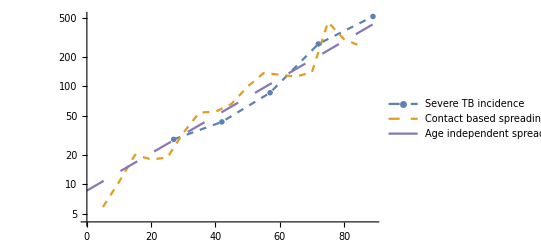

```mathematica
Show[ListLogPlot[{inc,Transpose[{Ages2,0.65incnorm Chop[Eigenvectors[Ems.(0FRACMreg+Transpose[FRACMreg])]][[1]]/Pop}]},PlotMarkers->{"OpenMarkers",None},Joined->True,PlotStyle->Dashed,PlotLegends->{"Severe TB incidence","Contact based spreading model"}],LogPlot[{None,None,None,None,Exp[lm[t]]},{t,0,100}, 
 PlotStyle -> { Dashing[Large]},PlotLegends->{None,None,None,None,"Age independent spreading model"}]]
```

```mathematica
(*  France COVID
```

```mathematica
Ages2=Range[5,85,10]
```

{5,15,25,35,45,55,65,75,85}

```mathematica
mexpshort=Table[Exp[0.044Ages2[[i]]]/10,{i,Length[Ages2]}]
```

{0.124608,0.193479,0.300417,0.466459,0.724274,1.12459,1.74615,2.71126,4.2098}

```mathematica
Ems=DiagonalMatrix[mexpshort]
```

{{0.124608,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.193479,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.300417,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.466459,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.724274,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.12459,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.74615,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.71126,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.2098}}

```mathematica
FRACMreg=Drop[Import["~/Projects/TB/CM/mat_regular_10_80_V2.csv"],1,1]
```

{{4.35489,1.12877,0.691601,1.86675,1.55005,0.742783,0.33222,0.122504,0.0376935},{0.830273,11.9953,0.956307,1.08197,2.34747,0.746988,0.240643,0.229956,0.0442223},{0.332464,1.81787,4.64244,1.71435,1.81732,1.46295,0.252497,0.209775,0.152813},{1.10587,0.885478,1.90724,3.19691,2.01082,0.781121,0.894823,0.253105,0.369923},{0.652141,0.879459,1.61731,2.51354,3.61472,2.38218,0.76021,0.570157,0.0698722},{0.313956,0.413972,1.42406,1.99766,2.63286,2.57192,1.14786,0.430531,0.772306},{0.289784,0.401014,0.549972,1.27199,1.31818,0.975378,2.21875,0.580869,0.267993},{0.176859,0.179432,0.591675,1.35764,1.44575,0.990413,1.2631,1.45796,0.562091},{0.19398,0.404126,0.815436,0.829805,0.995048,1.00044,1.21956,1.30218,0.964514}}

```mathematica
data=Drop[Import["/Users/user/Projects/TB/CM/France-2019.csv"],1,1]
```

{{1875383,1793838},{2011880,1925529},{2040340,1947414},{1974988,1894312},{1867826,1830692},{1843171,1873759},{1949911,2023620},{1981008,2053344},{1969854,2020238},{2187504,2230886},{2142209,2215992},{2062831,2179885},{1891456,2060753},{1793134,2013370},{1553223,1806321},{928599,1168168},{737011,1079459},{467972,845248},{192992,462602},{50390,164018},{2811,15788}}

```mathematica
agedirFRA=Table[Sum[data[[i,k]],{i,2j-1,2j},{k,2}],{j,1,9}]
```

{7606630,7857054,7415448,8007883,8408482,8600917,7758713,5456311,3129690}

```mathematica
agedirFRA[[9]]=Sum[data[[i,k]],{i,2j-1,2j},{k,2},{j,9,10}]
```

3999692

```mathematica
data=Import["~/Projects/TB/CM/francehosp.csv"]
```

{{reg,cl_age90,jour,hosp,rea,rad,dc},{1,0,18/03/2020,0,0,0,0},{1,9,18/03/2020,0,0,0,0},{1,19,18/03/2020,0,0,0,0},{1,29,18/03/2020,0,0,0,0},10882,{94,69,12/05/2020,11,4,30,2},{94,79,12/05/2020,18,4,35,13},{94,89,12/05/2020,12,0,32,25},{94,90,12/05/2020,8,0,13,11}}
 |  |  |  |

```mathematica
hospall=Drop[data[[All,6]],1]+Drop[data[[All,7]],1];
```

```mathematica
hosp=Table[Sum[hospall[[11 18 54+11i+j]],{i,0,17}],{j,1,11 }]
```

{74760,567,404,2091,3967,6279,10323,12851,14257,15900,7598}

```mathematica
hosppreLD=Table[Sum[hospall[[11 18 54+11i+j]],{i,0,17}],{j,1,11 }]
```

{74760,567,404,2091,3967,6279,10323,12851,14257,15900,7598}

```mathematica
hospdropfirst=Drop[hosp,1]
```

{567,404,2091,3967,6279,10323,12851,14257,15900,7598}

```mathematica
data=Drop[Import["/Users/user/Projects/TB/CM/France-2019.csv"],1,1]
```

{{1875383,1793838},{2011880,1925529},{2040340,1947414},{1974988,1894312},{1867826,1830692},{1843171,1873759},{1949911,2023620},{1981008,2053344},{1969854,2020238},{2187504,2230886},{2142209,2215992},{2062831,2179885},{1891456,2060753},{1793134,2013370},{1553223,1806321},{928599,1168168},{737011,1079459},{467972,845248},{192992,462602},{50390,164018},{2811,15788}}

```mathematica
Dimensions[data]
```

{21,2}

```mathematica
Pop=Flatten[{Table[Sum[data[[i,k]],{i,2j-1,2j},{k,2}],{j,1,10}]}]
```

{7606630,7857054,7415448,8007883,8408482,8600917,7758713,5456311,3129690,870002}

```mathematica
Pop[[10]]=Sum[data[[i,k]],{i,2 10-1,Length[data]},{k,2}]
```

888601

```mathematica
hospFRA=Transpose[{Range[5,95,10],100000hospdropfirst/Pop}]
```

{{5,5670000/760663},{15,20200000/3928527},{25,8712500/308977},{35,396700000/8007883},{45,313950000/4204241},{55,1032300000/8600917},{65,1285100000/7758713},{75,1425700000/5456311},{85,53000000/104323},{95,759800000/888601}}

```mathematica
normFRA=hospFRA[[6,2]]/Exp[0.044  55]

CMnormFRA=hospFRA[[4,2]]/( Ems.Chop[Eigenvectors[Ems.(FRACMreg+Transpose[FRACMreg])]][[1]]/agedirFRA)[[5]]
```

10.6726

-3.04051×10^9

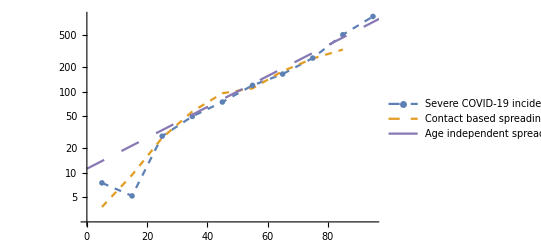

```mathematica
Show[ListLogPlot[{hospFRA,Transpose[{Ages2,-0.9CMnormFRA Chop[Eigenvectors[Ems.(0FRACMreg+Transpose[FRACMreg])]][[1]]/agedirFRA}]},PlotMarkers->{"OpenMarkers",None},Joined->True,PlotStyle->Dashed,PlotLegends->{"Severe COVID-19 incidence (hospitalization)","Contact based spreading model"}],LogPlot[{None,None,None,None,1.3Exp[lm[t]]},{t,0,100}, 
 PlotStyle -> { Dashing[Large]},PlotLegends->{None,None,None,None,"Age independent spreading model"}]]
```